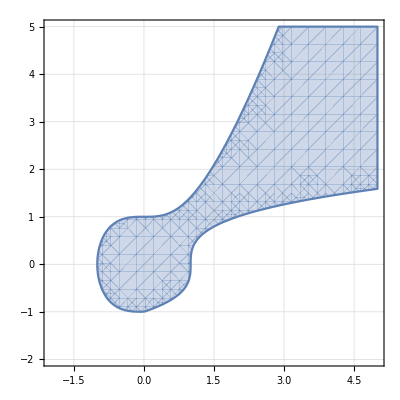

```mathematica
RegionPlot[{x<y^3+1&&y^2<x^3+1},{x,-2,5},{y,-2,5},GridLines->Automatic]
```

```mathematica
ListPlot[RegionPlot[{x^2<y^3+1&&y^2<x^3+1},{x,-2,5},{y,-2,5}][[1,1]]]
```

ListPlot::lpn: GraphicsComplex[{{-0.526316,-0.894737},{-0.157895,-0.894737},{0.210526,-0.894737},«6»,{-0.526316,-0.157895},«562»},{«1»}] 不是由数字或者数对组成的列表.

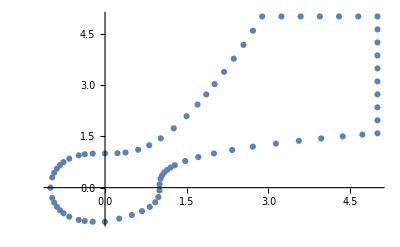

```mathematica
ListPlot@MeshCoordinates@BoundaryMesh@DiscretizeRegion@ParametricRegion[{{x,y},x<y^3+1&&y^2<x^3+1},{{x,-2,5},{y,-2,5}}]
```